```mathematica
(* F6Foray.nb: Some More Hadamards of Order 6 *)
(* A. J. Skinner, V. A. Newell, R. Sanchez *)
(* askinner at skidmore dot edu *)
(* 518-580-5127 *)
(* Skidmore College Physics, 815 North Broadway, Saratoga Springs, NY 12866, USA *)
```

```mathematica
(* This notebook numerically integrates the four parameter family described in *)(* "Unbiased bases (Hadamards) for six-level systems: Four ways from Fourier" *)
(* published in the Journal of Mathematical Physics, 50, 012107, 2009 *)
(* also available at http://arxiv.org/abs/0810.1761 *)
```

```mathematica
Ν=6; (* the order or Hilbert space dimension *)
(* here, the symbol "Ν" is obtained by typing "esc shift-N esc" *)
(* beware: this "Ν" is different from the "N" obtained by typing "shift-N" *)
```

```mathematica
(* the complex Hadamards of order Ν *)
(* are Ν x Ν unitary matrices of equimodular elements 1/(√Ν)ⅇ^(ⅈ Subscript[ϕ, im]) *)
```

```mathematica
(* here Subscript[ϕ, im] is the phase of the i^th component of the m^th column *)
(* m, n, o, p shall be column indices *)
(* i, j, k, l shall be row indices *)
(* throughout this notebook *)
```

```mathematica
(* we can represent a matrix of equimodular elements 1/(√Ν)ⅇ^(ⅈ Subscript[ϕ, im]) *)
(* by a matrix of its phases Subscript[ϕ, im] *)
phases[mat_]:=Arg[mat];
(* for example *)
MatrixForm[phases[1/(√2)({{1, -1}, {ⅈ, -ⅈ}})]]
```

(0 | π
π/2 | -π/2)

```mathematica
(* we can make a long vector (list) of phases from a matrix of phases *)
(* by concatenating 1st column, 2nd column, ... *)
longvec[mat_]:=Flatten[Transpose[mat]];
(* for example *)
longvec[phases[1/(√2)({{1, -1}, {ⅈ, -ⅈ}})]]
```

{0,π/2,π,-π/2}

```mathematica
(* here's the Fourier matrix written as a longvec (of phases) *)
fourier=longvec[Table[2π(j-1)(m-1)/Ν,{j,1,Ν},{m,1,Ν}]];
fourier=Mod[fourier,2π]
```

{0,0,0,0,0,0,0,π/3,(2 π)/3,π,(4 π)/3,(5 π)/3,0,(2 π)/3,(4 π)/3,0,(2 π)/3,(4 π)/3,0,π,0,π,0,π,0,(4 π)/3,(2 π)/3,0,(4 π)/3,(2 π)/3,0,(5 π)/3,(4 π)/3,π,(2 π)/3,π/3}

```mathematica
(* we can turn a longvec back into a candidate Hadamard matrix *)
candmat[lv_]:=1/(√Ν)Table[Exp[ⅈ lv[[Ν(m-1)+i]]],{i,1,Ν},{m,1,Ν}]
(* for example *)
MatrixForm[√6 candmat[fourier]]
```

(1 | 1 | 1 | 1 | 1 | 1
1 | ⅇ^((ⅈ π)/3) | ⅇ^((2 ⅈ π)/3) | -1 | ⅇ^(-(2 ⅈ π)/3) | ⅇ^(-(ⅈ π)/3)
1 | ⅇ^((2 ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3) | 1 | ⅇ^((2 ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3)
1 | -1 | 1 | -1 | 1 | -1
1 | ⅇ^(-(2 ⅈ π)/3) | ⅇ^((2 ⅈ π)/3) | 1 | ⅇ^(-(2 ⅈ π)/3) | ⅇ^((2 ⅈ π)/3)
1 | ⅇ^(-(ⅈ π)/3) | ⅇ^(-(2 ⅈ π)/3) | -1 | ⅇ^((2 ⅈ π)/3) | ⅇ^((ⅈ π)/3))

```mathematica
(* so we begin with Ν x Ν matrices of equimodular elements 1/(√Ν)(ⅇ^(ⅈ Subscript[ϕ, im]))^*)
(* whose columns are automatically unbiased with respect to the standard basis *)
(* and look for unitarity, i.e. for the columns to form an orthonormal basis *)
```

```mathematica
(* we define the nonunitarity "f" as proportional to the sum *)
(* over probabilities between nontrivial pairings of column vectors *)
(* f = (Ν^2/2) Sum[<Subscript[e, m]|Subscript[e, n]><Subscript[e, n]|Subscript[e, m]>,{m,1,Ν},{n,m+1,Ν}] *)
```

```mathematica
(* there is a constant part of the nonunitarity *)
f0=Sum[(* over mth and nth column vectors *)
Sum[(* over their jth = ith components *)
1/2,{i,1,Ν},{j,i,i}] 
,{m,1,Ν},{n,m+1,Ν}]
```

45

```mathematica
(* and a total nonunitary of a matrix of equimodular elements *)
(* here "lv" is a long vector of phases *)
f[lv_]:=Module[{f,m,n,i,j,im,jm,in,jn,arg,co},
f=f0;
Do[(* loop over mth and nth column vectors *)
Do[(* loop over their ith and jth components *)
(* solve for longvec indices from row and column indices *)
im=Ν(m-1)+i;jm=Ν(m-1)+j;in=Ν(n-1)+i;jn=Ν(n-1)+j;
(* find the overall argument, its cosine, and update f *)
arg=lv[[in]]-lv[[im]]+lv[[jm]]-lv[[jn]];
co=Cos[arg];f=f+co;
,{i,1,Ν},{j,i+1,Ν}];
,{m,1,Ν},{n,m+1,Ν}];
f (* returns the total nonunitarity *)
]
```

```mathematica
(* The Fourier matrix is unitary *)
f[fourier]
```

0

```mathematica
(* we will need to know how the nonunitarity varies as we vary the phases *)
(* so we need the gradient g and the Hessian h *)
g36=Table[0,{Ν^2}]; 
h36=Table[0,{Ν^2},{Ν^2}];
```

```mathematica
(* fgh[lv] finds the gradient and Hessian while figuring the nonunitarity *)
(* it takes longer than f[lv] but returns more useful information *)
(* again, "lv" is a longvec of phases *)
fgh[lv_]:=Module[
{f,m,n,i,j,im,jm,in,jn,arg,co,si,kos,kosigns,kocase,lps,lpsigns,lpcase},
f=f0;g36=0g36;h36=0h36;(* initialize f, g, h *)
Do[(* loop over mth and nth column vectors *)
Do[(* loop over their ith and jth components *)
(* solve for longvec indices from row and column indices *)
im=Ν(m-1)+i;jm=Ν(m-1)+j;in=Ν(n-1)+i;jn=Ν(n-1)+j;
(* find the overall argument, its cosine, its sine, and update f *)
arg=lv[[in]]-lv[[im]]+lv[[jm]]-lv[[jn]];
co=Cos[arg];si=Sin[arg];f=f+co;
(* now for the gradient and Hessian and all their Kronecker deltas *)
(* the -Sin[arg] only contributes to the gradient ∂f/∂Subscript[ϕ, ko] *)
(* when i=k & m=o (with a factor -1) *)
(* when j=k & m=o (with a factor 1) *)
(* when i=k & n=o (with a factor 1) *)
(* when j=k & n=o (with a factor -1) *)
(* so here is a list of the four scenarios *)
kos={im,jm,in,jn};kosigns={-1,1,1,-1};
(* the -Cos[arg] only contributes to the Hessian ∂^2 f/∂Subscript[ϕ, ko]∂Subscript[ϕ, lp] *)
(* per the aforementioned scenarios and *)
(* when furthermore i=l & m=p (with an additional factor -1) *)
(* when furthermore j=l & m=p (with an additional factor 1) *)
(* when furthermore i=l & n=p (with an additional factor 1) *)
(* when furthermore j=l & n=p (with an additional factor -1) *)
(* so here is a list of the four additional scenarios *)
lps={im,jm,in,jn};lpsigns={-1,1,1,-1};
(* and now we'll loop over the non-zero contributions *)
(* and add them into the right matrix elements of g and h *)
Do[ (* loop over the four gradient scenarios mentioned above *)
g36[[kos[[kocase]]]]=g36[[kos[[kocase]]]]-kosigns[[kocase]]si;
Do[(* loop over the additional four Hessian scenarios mentioned above *)
h36[[kos[[kocase]],lps[[lpcase]]]]=h36[[kos[[kocase]],lps[[lpcase]]]]-lpsigns[[lpcase]]kosigns[[kocase]]co;
,{lpcase,1,4}];
,{kocase,1,4}];
,{i,1,Ν},{j,i+1,Ν}];
,{m,1,Ν},{n,m+1,Ν}];
{f,g36,h36}
]
```

```mathematica
(* now let's try it out on the Fourier matrix's longvec of phases *)
(* the Fourier matrix is unitary, i.e. its nonunitarity f=0 *)
(* but the nonunitary varies with adjustments to the phases *)
(* not to first order, because fourier minimizes the nonunitarity, so g36=0 *)
(* but definitely to second order, so h36≠0 *)
{nonu,g36,h36}=fgh[fourier];
nonu
g36
MatrixForm[h36]
Eigenvalues[h36]
```

0

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

(5 | -1 | -1 | -1 | -1 | -1 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2
-1 | 5 | -1 | -1 | -1 | -1 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2
-1 | -1 | 5 | -1 | -1 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1
-1 | -1 | -1 | 5 | -1 | -1 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2
-1 | -1 | -1 | -1 | 5 | -1 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2
-1 | -1 | -1 | -1 | -1 | 5 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1
-1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | 5 | -1 | -1 | -1 | -1 | -1 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2
-1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1 | 5 | -1 | -1 | -1 | -1 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2
1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | -1 | -1 | 5 | -1 | -1 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1
1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | -1 | -1 | 5 | -1 | -1 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2
1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | -1 | -1 | -1 | -1 | 5 | -1 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2
-1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1 | -1 | -1 | -1 | -1 | 5 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1
-1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | 5 | -1 | -1 | -1 | -1 | -1 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1
1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1 | 5 | -1 | -1 | -1 | -1 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1 | -1 | 1 | -1 | 1 | -1
1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | -1 | -1 | 5 | -1 | -1 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1 | 1 | -1 | 1 | -1 | 1
-1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | -1 | -1 | 5 | -1 | -1 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | -1 | 1 | -1 | 1 | -1
1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | -1 | -1 | -1 | -1 | 5 | -1 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1
1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1 | -1 | -1 | -1 | -1 | 5 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | -1
-1 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | 5 | -1 | -1 | -1 | -1 | -1 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2
1 | -1 | 1 | -1 | 1 | -1 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1 | 5 | -1 | -1 | -1 | -1 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2
-1 | 1 | -1 | 1 | -1 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | -1 | -1 | 5 | -1 | -1 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1
1 | -1 | 1 | -1 | 1 | -1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | -1 | -1 | 5 | -1 | -1 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2
-1 | 1 | -1 | 1 | -1 | 1 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | -1 | -1 | -1 | -1 | 5 | -1 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2
1 | -1 | 1 | -1 | 1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1 | -1 | -1 | -1 | -1 | 5 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1
-1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | 5 | -1 | -1 | -1 | -1 | -1 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2
1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1 | 5 | -1 | -1 | -1 | -1 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2
1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | -1 | -1 | 5 | -1 | -1 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1
-1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | -1 | -1 | 5 | -1 | -1 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2
1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | -1 | -1 | -1 | -1 | 5 | -1 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2
1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1 | -1 | -1 | -1 | -1 | 5 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1
-1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | 5 | -1 | -1 | -1 | -1 | -1
-1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1 | 5 | -1 | -1 | -1 | -1
1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | 1 | -1 | -1 | 5 | -1 | -1 | -1
1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | -1 | -1 | 5 | -1 | -1
1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1/2 | -1 | -1 | -1 | -1 | 5 | -1
-1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1/2 | 1/2 | -1 | 1/2 | 1/2 | -1 | -1/2 | 1/2 | 1 | 1/2 | -1/2 | -1 | -1 | -1 | -1 | -1 | -1 | 5)

{12,12,12,12,12,9,9,9,9,9,9,9,9,9,9,9,9,3,3,3,3,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
(* longvecs, or candidate hadamards, live in an Ν^2 dimensional space of phases *)
(* here are two directions in which one can move away from fourier *)
(* corresponding to the first fourier family *)
phi12=1/(√6)({{0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 1, 0, 1}});
(* here are two more directions, corresponding to the second fourier family *)
phi34=1/(√6)({{0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0}, {0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1, 0, 0, 0, 0, 0, 0, 0, 0, 1, 0, 0, 1}});
(* here's a list of all four of those directions *)
MatrixForm[√6(phi1234=Join[phi12,phi34])]
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1)

```mathematica
(* those four directions are in the fourier Hessian's nullspace *)
(* i.e. moving in any one of those directions doesn't change the nonunitarity *)
(* to second order  *)
MatrixForm[h36.Transpose[phi1234]]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

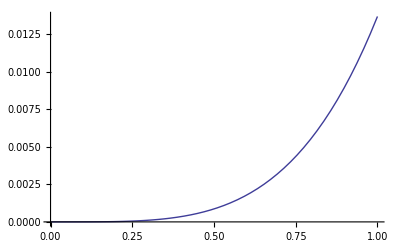

```mathematica
(* while those four directions span the nullspace *)
(* they are not necessarily compatible *)
(* there is, for example, a quartic contribution to the nonunitarity *)
(* when moving in the phi2+phi3 direction *)
Plot[f[fourier+th (phi1234[[2]]+phi1234[[3]])/√2],{th,0,1}]
```

```mathematica
(* in quantum mechanics the overall phase of a state vector is irrelevant *)
(* so for each column vec we can constrain its first phase (to be zero) *)
(* in which case we can ignore the partials with respect to those phases *)
(* and concentrate on the others *)
(* here are the relevant indices from an Ν^2-element longvec *)
MatrixForm[im30=Table[Ν(m-1)+i,{i,2,Ν},{m,1,Ν}]]
im30=Flatten[Transpose[im30]]
(* which we can use to concentrate on the relevant partials as follows *)
g30=g36[[im30]];
h30=h36[[im30,im30]];
```

(2 | 8 | 14 | 20 | 26 | 32
3 | 9 | 15 | 21 | 27 | 33
4 | 10 | 16 | 22 | 28 | 34
5 | 11 | 17 | 23 | 29 | 35
6 | 12 | 18 | 24 | 30 | 36)

{2,3,4,5,6,8,9,10,11,12,14,15,16,17,18,20,21,22,23,24,26,27,28,29,30,32,33,34,35,36}

```mathematica
(* we can also constrain the first phase of each row *)
(* according to the overall phase irrelevance of each standard basis vector *)
(* in which case we can also ignore the partials with respect to those phases *)
(* and concentrate on the others *)
(* here are the relevant indices from an Ν^2-element longvec *)MatrixForm[im25=Table[Ν(m-1)+i,{i,2,Ν},{m,2,Ν}]]
im25=Flatten[Transpose[im25]]
(* which we can use to concentrate on the relevant partials as follows *)
g25=g36[[im25]];
h25=h36[[im25,im25]];
```

(8 | 14 | 20 | 26 | 32
9 | 15 | 21 | 27 | 33
10 | 16 | 22 | 28 | 34
11 | 17 | 23 | 29 | 35
12 | 18 | 24 | 30 | 36)

{8,9,10,11,12,14,15,16,17,18,20,21,22,23,24,26,27,28,29,30,32,33,34,35,36}

```mathematica
(* starting from fourier, there are four directions in which we can move *)
(* here we take small steps in the first direction, then in the second, and so on *)
(* after each step we make small corrections with Newton's method *)
(* and update the four directions by projecting them into the changing nullspace *)
(* F6Foray takes a four element list, "thetas", specifying the distance to move in each dir *)
(* and returns the final nonunitarity at the end of the foray *)
(* it also records tracking data to review the foray after completion *)
F6Foray[thetas_]:=Module[
(* here is the list of variables used only within this Module *)
{phivec,dirvecs,dth,dths,mincurv,maxnewt,evals,evecs,n25,evecs36},

(* specify initial Hadamard and directions and integration parameters *)
phivec=N[fourier]; (* start at fourier for the initial hadamard *)
dirvecs=phi1234; (* start with phi1234 for the four normalized directions *)
dth=10^-3//N;(* small (slow) step size, in radians, in nullspace *)
dth=10^-1//N;(* big (fast) step size, in radians, in nullspace *)
dth=10^-2//N;(* medium (moderate) step size, in radians, in nullspace *)
nsteps=Round[Abs[thetas/dth]]; (* number of steps in each direction *)
dths=Table[thetas[[dir]]/nsteps[[dir]],{dir,1,4}];(* exact dth to use for each direction *)
mincurv=10^-4//N; (* minimum curvature for Newton's Method corrective step *)
maxnewt=10^-2 dth; (* maximum step size, in radians, for corrective step *)

(* here is a way to keep track of the four way foray from fourier *)
cntr=1;(* step index for tracking data *)
track=Table[{{0,0,0,0},fgh[phivec][[1]],phivec,dirvecs},{Total[nsteps]+1}]; 
(* first slot is for the accumulated phase shifts (thetas) in each direction *)
(* second slot is for the nonunitarity *)
(* third slot is for the current phases (phivec) *)
(* fourth slot is for the four evolving directions (dirvecs) *)

(* here, at last, is the four way foray from fourier *)
Do[ (* loop over the four directions *)
Do[ (* walk a distance thetas[[dir]] in the dirvecs[[dir]] direction *)

phivec=phivec+dths[[dir]] dirvecs[[dir]]; (* take a small step *)
{nonu,g36,h36}=fgh[phivec];(* evaluate *)

(* figure a corrective Newton Step as follows *)
g25=g36[[im25]];h25=h36[[im25,im25]]; (* focus on unconstrained phases *)
{evals,evecs}=Eigensystem[h25]; (* get the curvatures and principal axes *)
evecs=Orthogonalize[evecs,Method->GramSchmidt]; (* make sure degenerate ones are orthogonal *)
g25=evecs.g25; (* transform into eigenbasis of h25 *)
n25=Table[ (* figure newton step *)
If[Abs[evals[[alp]]]>mincurv,-g25[[alp]]/evals[[alp]],0],{alp,1,(Ν-1)^2}];(* note that mincurv prevents wild step in dir of almost zero curvature *)
If[Sqrt[n25.n25]>maxnewt,Print["Warning!!!!!   Large Newton Step = ", Sqrt[n25.n25]]];
n25=Transpose[evecs].n25; (* transform back into original basis *)

phivec[[im25]]=phivec[[im25]]+n25; (* take the newton step *)
{nonu,g36,h36}=fgh[phivec];(* evaluate *)

(* figure the new nullspace as follows *)
g25=g36[[im25]];h25=h36[[im25,im25]]; (* focus on unconstrained phases *)
{evals,evecs}=Eigensystem[h25]; (* get the curvatures and principal axes *)
evecs=(evecs[[Ordering[evals]]])[[1;;4]]; (* take 4D nullspace *)
evecs=Orthogonalize[evecs,Method->GramSchmidt];(* make sure degenerate dirs are orthogonal *)
evals=(Sort[evals])[[1;;4]]; (* check nullspace curvatures (should all be zero) *)
If[Total[Abs[evals]/4]>mincurv,
Print["Warning!!!!!   Nullspace Average Curvature = ",Total[Abs[evals]/4]]];

(* project the four directions into the new nullspace and normalize *)
evecs36=Table[0,{4},{36}];evecs36[[1;;4,im25]]=evecs; (* expand into Ν^2-element longvecs *)
dirvecs=Table[Sum[evecs36[[jdx]] (evecs36[[jdx]].dirvecs[[idx]]),{jdx,1,4}],{idx,1,4}];
Do[dirvecs[[idx]]=dirvecs[[idx]]/Sqrt[dirvecs[[idx]].dirvecs[[idx]]],{idx,1,4}];

(* record tracking data *)
cntr=cntr+1;
track[[cntr,1]]=track[[cntr-1,1]];track[[cntr,1,dir]]=th;
track[[cntr,2]]=nonu;
track[[cntr,3]]=phivec;
track[[cntr,4]]=dirvecs;

(* here is a line of code to print out some tracking data every ten steps *)
If[Mod[cntr,10]==0,Print[track[[cntr,1;;2]]]]

,{th,dths[[dir]],thetas[[dir]],dths[[dir]]}];
,{dir,1,4}];
nonu (* return the final nonunitarity, which should be negligible if all went well *)
]
```

```mathematica
(* here is an example *)
F6Foray[{1.31,-2.33,-1.101,2.17}]
```

{{0.09,0,0,0},7.77156×10^-16}

{{0.19,0,0,0},5.21805×10^-15}

{{0.29,0,0,0},-6.21725×10^-15}

{{0.39,0,0,0},-9.54792×10^-15}

{{0.49,0,0,0},-1.4766×10^-14}

{{0.59,0,0,0},-1.44329×10^-15}

{{0.69,0,0,0},-1.9873×10^-14}

{{0.79,0,0,0},-6.66134×10^-15}

{{0.89,0,0,0},-3.36398×10^-14}

{{0.99,0,0,0},-5.77316×10^-15}

{{1.09,0,0,0},-6.66134×10^-16}

{{1.19,0,0,0},-9.65894×10^-15}

{{1.29,0,0,0},1.11022×10^-16}

{{1.31,-0.08,0,0},1.38778×10^-14}

{{1.31,-0.18,0,0},8.32667×10^-15}

{{1.31,-0.28,0,0},3.55271×10^-15}

{{1.31,-0.38,0,0},-5.21805×10^-15}

{{1.31,-0.48,0,0},-8.54872×10^-15}

{{1.31,-0.58,0,0},1.11022×10^-15}

{{1.31,-0.68,0,0},1.36557×10^-14}

{{1.31,-0.78,0,0},-7.99361×10^-15}

{{1.31,-0.88,0,0},1.89848×10^-14}

{{1.31,-0.98,0,0},7.99361×10^-15}

{{1.31,-1.08,0,0},1.79856×10^-14}

{{1.31,-1.18,0,0},2.28706×10^-14}

{{1.31,-1.28,0,0},7.88258×10^-15}

{{1.31,-1.38,0,0},2.56462×10^-14}

{{1.31,-1.48,0,0},9.54792×10^-15}

{{1.31,-1.58,0,0},2.23155×10^-14}

{{1.31,-1.68,0,0},1.23235×10^-14}

{{1.31,-1.78,0,0},-3.9968×10^-15}

{{1.31,-1.88,0,0},1.32117×10^-14}

{{1.31,-1.98,0,0},-6.99441×10^-15}

{{1.31,-2.08,0,0},2.06501×10^-14}

{{1.31,-2.18,0,0},2.63123×10^-14}

{{1.31,-2.28,0,0},6.99441×10^-15}

{{1.31,-2.33,-0.0500455,0},3.09752×10^-14}

{{1.31,-2.33,-0.150136,0},3.71925×10^-14}

{{1.31,-2.33,-0.250227,0},-9.54792×10^-15}

{{1.31,-2.33,-0.350318,0},7.10543×10^-15}

{{1.31,-2.33,-0.450409,0},-2.24265×10^-14}

{{1.31,-2.33,-0.5505,0},-1.11022×10^-16}

{{1.31,-2.33,-0.650591,0},-5.9952×10^-15}

{{1.31,-2.33,-0.750682,0},1.63203×10^-14}

{{1.31,-2.33,-0.850773,0},1.68754×10^-14}

{{1.31,-2.33,-0.950864,0},-3.63043×10^-14}

{{1.31,-2.33,-1.05095,0},-3.64153×10^-14}

{{1.31,-2.33,-1.101,0.05},1.88738×10^-15}

{{1.31,-2.33,-1.101,0.15},1.69864×10^-14}

{{1.31,-2.33,-1.101,0.25},4.00791×10^-14}

{{1.31,-2.33,-1.101,0.35},1.12133×10^-14}

{{1.31,-2.33,-1.101,0.45},3.01981×10^-14}

{{1.31,-2.33,-1.101,0.55},3.61933×10^-14}

{{1.31,-2.33,-1.101,0.65},1.79856×10^-14}

{{1.31,-2.33,-1.101,0.75},-2.55351×10^-15}

{{1.31,-2.33,-1.101,0.85},6.21725×10^-15}

{{1.31,-2.33,-1.101,0.95},2.30926×10^-14}

{{1.31,-2.33,-1.101,1.05},-1.40998×10^-14}

{{1.31,-2.33,-1.101,1.15},3.55271×10^-15}

{{1.31,-2.33,-1.101,1.25},-1.80966×10^-14}

{{1.31,-2.33,-1.101,1.35},-2.42029×10^-14}

{{1.31,-2.33,-1.101,1.45},4.4964×10^-14}

{{1.31,-2.33,-1.101,1.55},-6.99441×10^-15}

{{1.31,-2.33,-1.101,1.65},1.42109×10^-14}

{{1.31,-2.33,-1.101,1.75},-1.9873×10^-14}

{{1.31,-2.33,-1.101,1.85},-5.77316×10^-15}

{{1.31,-2.33,-1.101,1.95},-3.33067×10^-16}

{{1.31,-2.33,-1.101,2.05},2.10942×10^-15}

{{1.31,-2.33,-1.101,2.15},1.40998×10^-14}

3.66374×10^-15

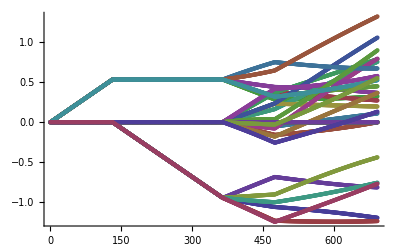

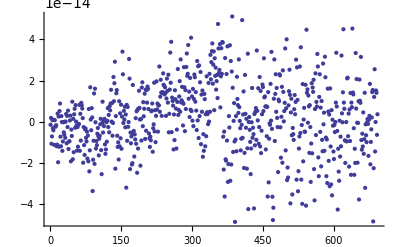

```mathematica
(* here are plots of the phase shifts and nonunitarity during the foray *)
deltaphivecs=track[[1;;cntr,3]]-Table[fourier,{cntr}];
ListPlot[Transpose[deltaphivecs],PlotRange->All]
ListPlot[track[[1;;cntr,2]],PlotRange->All]
```

```mathematica
(* and here is the final hadamard *)
MatrixForm[final=candmat[track[[cntr,3]]]]
(* comprising equimodular elements *)
MatrixForm[√6 Abs[final]]
(* of various phases *)
MatrixForm[Arg[final]]
(* and looking very nicely unitary *)
MatrixForm[Chop[Transpose[Conjugate[final]].final,10^-6]]
```

(0.408248+0. ⅈ | 0.408248+0. ⅈ | 0.408248+0. ⅈ | 0.408248+0. ⅈ | 0.408248+0. ⅈ | 0.408248+0. ⅈ
0.408248+0. ⅈ | 0.0811321+0.400105 ⅈ | 0.118778+0.390587 ⅈ | -0.4004-0.0796659 ⅈ | 0.0609439-0.403674 ⅈ | -0.268702-0.307353 ⅈ
0.408248+0. ⅈ | -0.241305+0.3293 ⅈ | -0.101466-0.395438 ⅈ | 0.28717+0.290172 ⅈ | -0.364409+0.184045 ⅈ | 0.0117626-0.408079 ⅈ
0.408248+0. ⅈ | -0.38105-0.146517 ⅈ | 0.369025-0.174605 ⅈ | -0.199145-0.356382 ⅈ | 0.0987195+0.396133 ⅈ | -0.295798+0.281372 ⅈ
0.408248+0. ⅈ | -0.204588-0.353285 ⅈ | -0.391163+0.116869 ⅈ | 0.285337+0.291975 ⅈ | 0.150763-0.379391 ⅈ | -0.248596+0.323831 ⅈ
0.408248+0. ⅈ | 0.337564-0.229603 ⅈ | -0.403422+0.0625867 ⅈ | -0.381211-0.1461 ⅈ | -0.354265+0.202887 ⅈ | 0.393086+0.110229 ⅈ)

(1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1.
1. | 1. | 1. | 1. | 1. | 1.)

(0. | 0. | 0. | 0. | 0. | 0.
0. | 1.37073 | 1.27558 | -2.94519 | -1.42095 | -2.2892
0. | 2.20319 | -1.82197 | 0.790599 | 2.67391 | -1.54198
0. | -2.77451 | -0.44194 | -2.08037 | 1.32656 | 2.38118
0. | -2.09571 | 2.85126 | 0.796897 | -1.19255 | 2.22551
0. | -0.597297 | 2.98768 | -2.77561 | 2.62149 | 0.273398)

(1. | 0 | 0 | 0 | 0 | 0
0 | 1. | 0 | 0 | 0 | 0
0 | 0 | 1. | 0 | 0 | 0
0 | 0 | 0 | 1. | 0 | 0
0 | 0 | 0 | 0 | 1. | 0
0 | 0 | 0 | 0 | 0 | 1.)